# 4T Modelling Thermodynamics and Equilibrium of mixture of radiation field, ionic gas and electron gas

## Constants and Functions

electron-ion collision cross sections
typically 10^(-11) m^2
https://www.nist.gov/system/files/documents/srd/jpcrd386.pdf

Permittivity of Free Space (ε₀):

SI Unit: $$\varepsilon_0 = 8.854 \times 10^{-12} \, \text{F/m}$$ (Farads per meter)

CGS Unit: $$\varepsilon_0 = 1$$ (dimensionless, since in the CGS system, the permittivity of free space is typically taken as 1)

Boltzmann Constant (k):

SI Unit: $$k = 1.381 \times 10^{-23} \, \text{J/K}$$ (Joules per Kelvin)

CGS Unit: $$k = 1.381 \times 10^{-16} \, \text{erg/K}$$ (ergs per Kelvin)

Charge of the Electron (e):

SI Unit: $$e = 1.602 \times 10^{-19} \, \text{C}$$ (Coulombs)

CGS Unit: $$e = 4.803 \times 10^{-10} \, \text{statC}$$ (statcoulombs)


1 erg = $$6.242 \times 10^{11} \, \text{eV}$$

So, to convert ergs to electron volts, you multiply the number of ergs by $$6.242 \times 10^{11}$$. Conversely, to convert electron volts to ergs, you divide the number of eV by $$6.242 \times 10^{11}$$.
a=8*pi^.065 / (.0115h^3c^3)
a=4 sigmasb/c.02

```mathematica
(* Initial parameters and constants *)

(*


*)

c= 3.0*10^(6);
ep0 = 1.0; (* 8.8541878128*10^(−12);*)
kb = 1.380649*10^(−16);
ee = 4.803*10^(-10);
na=6.02*10^23; (* avogadros number*)

a = 2*10^(-8);
mp = 1.67262192*10^(-24);
md = 2.014102*mp;(*mass deuterium*)
mt= 3.016049*mp;(*mass tritium*)
mal = 4.002603*mp; (**)
hbar = 1.05457182 *10^(-27);
me = 9.1093837*10^(-28);
mme=me*na; (* molar electron mass*)
ui = 13.6 * ee;(* ionization energy for hydrogen*)

ar = 5.670374*10^(-5) ;(* stefan-boltzmann constant *)

sigmaie = 1.0*10^(-7); (* e- ion collision cross section  cm^2*)
sigmaii  = Pi*a*a; (* ion ion collision cross section based on atomic size *)

(*Nuclear Constants for burning and transfer*)
sigt= (8/Pi)*(ee^2/(me*c*c))^2;  (*thompson cross section*)  
kevtok = 11604525.0061657; (* convert kev to kelvin*)
```

3.×10^8

## Model Parameters

```mathematica
{{(*The model parameters*)
Ni=1; (* number of moles of ions in total*)
ni0 =Ni*na; (*initial number of moles of ions*)(*  amount of D and T *)
ne=2*ni0;  (* number of electrons*)

niini=1*na;te0=1.6; ti=1.6;
t0=0;
tf=1*10^(-15);  (*0.0002;*)(*final time*)
h=1*(10)^(-17);(*step size*)}, {□}}
```

{{Null^7},{□}}

```mathematica
{{(* Saha equation*) (* Here calculate the ionization fraction *)
x[N_,T_, Ne_]:= ((2*Pi*me*kb/hbar)^(3/2))*(T^(3/2)/Ne)*Exp[-(ui/(kb*T))]; (* Ne is electron number density *) (* typical ne 10^(-20)*)

(* time between collisions ... relaxation time*)
taun[N_,T_]:=(1/(N*sigmaii))*Sqrt[mp/(kb*T)];
taue[Ne_,Te_]:=(1/(Ne*sigmaie))*Sqrt[me/(kb*Te)]}, {□}}
```

{{Null^3},{□}}

## Radiation and Perfect Gas

and Gas Perfect Radiation

```mathematica
pr[N_, Vo_, T_]:= (N*kb*T/Vo)+(ar*T^4)/3;
Et[N_,Vo_,T_]:= (3/2)*(N*kb*T)+(Vo*ar*T^4);
St[N_,Vo_,T_]:= N*kb*Log[Vo*T^(3/2)]+(4/3)*ar*Vo*T^3
```

## Radiation and Ionic Gas

```mathematica
(*   using saha equation  to get energy and pressure for ionic gas and radiation field*)
```

## Planck and Bose Einstein Distribution

```mathematica
(*  Planck distribution*)
```

```mathematica
npl[nu_,T_]:= 1.0/(Exp[2*Pi*hbar*nu/(kb*T)]-1.0)
```

```mathematica
(* Bose-Einstein distribution*)
```

```mathematica
nbe[nu_,mu_,T_]:= 1.0/(Exp[((2*Pi*hbar*nu)/(kb*T))-mu]-1.0)
```

```mathematica
fbe[ep_,al_]:= 1.0/(Exp[ep+al]-1.0);
```

## Rates for Nuclear Reactions

```mathematica
(* rates for nuclear reactions*)
```

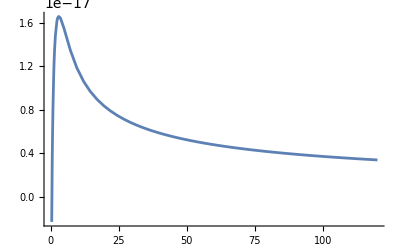

9.55942×10^-18 1.16612×10^-17 6.75524×10^-18  5.23259×10^-18

```mathematica
Adt=10*5.0*10^(-18);  (*cm^2*)(* m^3/s*)
kdt=0.6;
T0dt=0.74;
sigvdt[T_]:=Adt*(T0dt-Exp[-kdt*T])/Sqrt[T];(*DT fusion reaction cross section sigv*) (*T is the temperature in keV*)
Plot[sigvdt[x1],{x1,0,120}] 
Print[sigvdt[1]," ",sigvdt[10]," ",sigvdt[30],"  ",sigvdt[50]] ;
```

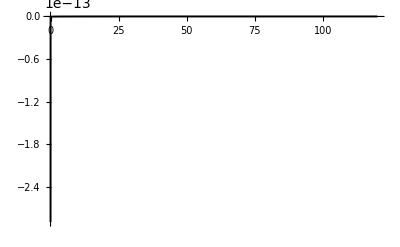

```mathematica
Plot[sigvdt[x1],{x1,0,120},PlotRange->All]
```

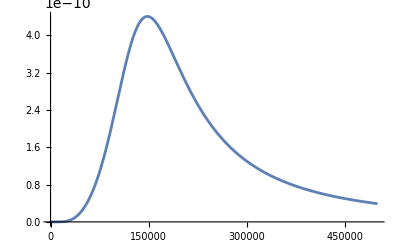

```mathematica
AFC =325*(10)^(-3)*(10^8);
FCC=10^(-28);
GAFC=71.7*(10^3);
ERFC =124.3*(10^3);
sigvdtfc[T_]:=(1/T)*(AFC/((ERFC-T)^2+GAFC^2))*Exp[-1.72*(10^3)/Sqrt[T]]
Plot[sigvdtfc[x1],{x1,0,500000}]
```

```mathematica
"interactive plot"%62DynamicModule[{xc,dx},Manipulate[Plot[sigvdt[x1],{x1,xc-dx,xc+dx}],{{xc,60,"center"},-300,420},{{dx,60.,"zoom"},360,3.6}],DynamicModuleValues:>{}]
```

```mathematica
(* functions *)
nuc[ne_] := c*sigt*ne(* compton strength*);
lambda[te_,ne_]:= 25.127-Log[(ne^0.5)/(1000.0*te)];  (* keV *)
fali[te_]:= (te)/((te)+32);
eal:= ee*3.5*(10^6);(*MeV*)
al:=0.01;
em:=99999.0;


(*mme molar mass of electron*)
pei[ne_, ni_,te_,ti_]:=(6/Sqrt[Pi])*nuc[ne]*ni*((mme/md)+(mme/mt)+4*((ni0-ni)/ni)*(mme/mal))*((me*c*c/(2*te))^(3/2))*Log[lambda[te,ne]]*(ti-te);
```

## Radiation Solver Section

```mathematica
(**)
k0[x]:=1.0;
Ib[alph_,gam_]:= ∫_0^em k0[x/2]*Exp[-x/2]*(Exp[alph+(x/gam)]-Exp[x])/(Exp[alph+(x/gam)]-1)ⅆx;(*complete this with integral definition*)
(**)
Ic[alph_,gam_]:= (1-gam)*∫_0^em (x^4)*Exp[alph+x]/(Exp[alph+x]-1)^2ⅆx;(*complete this with integral definition*)
(**)
f[alph_, tr_, te_ ]:=  (1.0/(4*(1-gam))*Ic[alph,tr/te] ;
```

```mathematica
(**)
prad[ni_,te_,ti_,tr_]:= tr^4;
```

```mathematica
(**)
```

```mathematica
(**)
```

## Rates of Change of ni, Te and Ti CHECK THE UNITS

```mathematica
f1[t_,ni_,te_,ti_]:=-(ni^2)*sigvdt[ti/kevtok];      (* dni/dt *)
f2[t_,ni_,te_,ti_]:=kevtok*(2/(3*ne))*((eal*(1-fali[te/kevtok]))*(ni^2)*sigvdt[ti/kevtok]   +pei[ne,ni,te,ti]  );(* dte/dt *) 
f3[t_,ni_,te_,ti_]:=kevtok*(2/(3*(ni+ni0)))*((eal*fali[te/kevtok]+(3*ti/2))*(sigvdt[ti/kevtok]*ni^2)-pei[ne,ni,te,ti]); (* dti/dt *)
```

```mathematica
Print[pei[ne,niini,te0*kevtok,ti*kevtok],"  ",nuc[ne]];
Print[f1[h,niini,te0*kevtok,ti*kevtok]];
Print[f2[h,niini,te0*kevtok,ti*kevtok]];
Print[f3[h,niini,te0*kevtok,ti*kevtok]];
```

0.  7.28241×10^21

-5.11566×10^30

5.26263×10^10

9.15482×10^20

```mathematica
(*Runge-Kutta method implementation for the coupled system*)
rk4Step[t_,ni_,te_,ti_,h_]:=Module[{k1,k2,k3,k4,l1,l2,l3,l4,m1,m2,m3,m4},
k1=h f1[t,ni,te,ti];
l1=h f2[t,ni,te,ti];
m1=h f3[t,ni,te,ti];

k2=h f1[t+h/2,ni+k1/2,te+l1/2, ti+m1/2];
l2=h f2[t+h/2,ni+k1/2,te+l1/2, ti+m1/2];
m2=h f3[t+h/2,ni+k1/2,te+l1/2, ti+m1/2];

k3=h f1[t+h/2,ni+k2/2,te+l2/2,ti+m2/2];
l3=h f2[t+h/2,ni+k2/2,te+l2/2,ti+m2/2];
m3=h f3[t+h/2,ni+k2/2,te+l2/2,ti+m2/2];

k4=h f1[t+h,ni+k3,te+l3, ti+m3];
l4=h f2[t+h,ni+k3,te+l3, ti+m3];
m4=h f3[t+h,ni+k3,te+l3, ti+m3];

{ni+(k1+2 k2+2 k3+k4)/6,te+(l1+2 l2+2 l3+l4)/6  ,ti+(m1+2 m2+2 m3+m4)/6  }];

Print[niini," ",te0," ",ti," ",h];
```

6.02×10^23 1.6 1.6 1/100000000000000000

```mathematica
{ni,te,tine}=rk4Step[0,niini,te0*kevtok,ti*kevtok,h];
Print[ni];
Print[te/kevtok];
Print[tine/kevtok];
```

6.02×10^23

1.60154

1.59925

```mathematica
{ni,te,tine}=rk4Step[h,ni,te,tine,h];
Print[ni];
Print[te/kevtok];
Print[tine/kevtok];
```

6.02×10^23

1.6209

1.58068

```mathematica
{ni,te,tine}=rk4Step[h,ni,te,tine,h];
Print[ni];
Print[te/kevtok];
Print[tine/kevtok];
```

6.02×10^23

2.16328

1.03913

```mathematica
{ni,te,ti}=rk4Step[t,ni,te,ti,h];
```

```mathematica
rk4Solve[t0_,niini_,te0_, ti0_ ,h_,tf_]:=Module[{t=t0,ni=niini,te=te0, ti=ti0,sol={{t0,niini,te0, ti0}}},
While[t<tf,
{ni,te,ti}=rk4Step[t,ni,te,ti,h];
t=t+h;
Print[t," ",ni," ",te/kevtok," ",ti/kevtok];
AppendTo[sol,{t,ni,te,ti}];];sol];
Print[h,t0,tf];
```

1/100000000000000000 0 1/1000000000000000

```mathematica
(*Solve the coupled differential equations*)
solution=rk4Solve[t0,niini,te0*kevtok,ti*kevtok,h,tf];
```

1/100000000000000000 6.02×10^23 1.60154 1.59925

1/50000000000000000 6.02×10^23 1.6209 1.58068

3/100000000000000000 6.02×10^23 2.16328 1.03913

1/25000000000000000 6.02×10^23-5.0438×10^13 ⅈ 1.50922+4.91276 ⅈ 1.69399-4.91293 ⅈ

1/20000000000000000 6.02×10^23-8.14393×10^13 ⅈ -2.38075+7.24345 ⅈ 5.58745-7.24548 ⅈ

3/50000000000000000 6.02×10^23-9.9552×10^13 ⅈ -4.99611+9.99864 ⅈ 8.2067-10.0024 ⅈ

7/100000000000000000 6.02×10^23-1.1447×10^14 ⅈ -7.00955+12.5209 ⅈ 10.2246-12.5268 ⅈ

1/12500000000000000 6.02×10^23-1.28179×10^14 ⅈ -8.72268+14.8373 ⅈ 11.9426-14.8456 ⅈ

9/100000000000000000 6.02×10^23-1.4107×10^14 ⅈ -10.2518+16.9962 ⅈ 13.477-17.007 ⅈ

1/10000000000000000 6.02×10^23-1.53308×10^14 ⅈ -11.6539+19.0317 ⅈ 14.8847-19.0451 ⅈ

11/100000000000000000 6.02×10^23-1.65021×10^14 ⅈ -12.9615+20.9674 ⅈ 16.1981-20.9838 ⅈ

3/25000000000000000 6.02×10^23-1.76303×10^14 ⅈ -14.1951+22.8204 ⅈ 17.4377-22.8397 ⅈ

13/100000000000000000 6.02×10^23-1.87219×10^14 ⅈ -15.3686+24.6031 ⅈ 18.6176-24.6256 ⅈ

7/50000000000000000 6.02×10^23-1.97818×10^14 ⅈ -16.4922+26.3252 ⅈ 19.7477-26.3509 ⅈ

3/20000000000000000 6.02×10^23-2.08138×10^14 ⅈ -17.5732+27.9941 ⅈ 20.8355-28.0233 ⅈ

1/6250000000000000 6.02×10^23-2.18208×10^14 ⅈ -18.6173+29.616 ⅈ 21.8865-29.6486 ⅈ

17/100000000000000000 6.02×10^23-2.28052×10^14 ⅈ -19.6292+31.1958 ⅈ 22.9054-31.232 ⅈ

9/50000000000000000 6.02×10^23-2.37691×10^14 ⅈ -20.6123+32.7375 ⅈ 23.8958-32.7774 ⅈ

19/100000000000000000 6.02×10^23-2.47143×10^14 ⅈ -21.5697+34.2447 ⅈ 24.8607-34.2883 ⅈ

1/5000000000000000 6.02×10^23-2.56422×10^14 ⅈ -22.5039+35.7202 ⅈ 25.8024-35.7677 ⅈ

21/100000000000000000 6.02×10^23-2.65541×10^14 ⅈ -23.417+37.1666 ⅈ 26.7232-37.2181 ⅈ

11/50000000000000000 6.02×10^23-2.74511×10^14 ⅈ -24.3107+38.5861 ⅈ 27.6248-38.6416 ⅈ

23/100000000000000000 6.02×10^23-2.83342×10^14 ⅈ -25.1867+39.9806 ⅈ 28.5088-40.0402 ⅈ

3/12500000000000000 6.02×10^23-2.92043×10^14 ⅈ -26.0462+41.3518 ⅈ 29.3764-41.4156 ⅈ

1/4000000000000000 6.02×10^23-3.00621×10^14 ⅈ -26.8904+42.7013 ⅈ 30.2289-42.7693 ⅈ

13/50000000000000000 6.02×10^23-3.09084×10^14 ⅈ -27.7204+44.0302 ⅈ 31.0672-44.1026 ⅈ

27/100000000000000000 6.02×10^23-3.17437×10^14 ⅈ -28.5371+45.3399 ⅈ 31.8923-45.4167 ⅈ

7/25000000000000000 6.02×10^23-3.25687×10^14 ⅈ -29.3412+46.6315 ⅈ 32.7051-46.7128 ⅈ

29/100000000000000000 6.02×10^23-3.33838×10^14 ⅈ -30.1336+47.9058 ⅈ 33.5062-47.9917 ⅈ

3/10000000000000000 6.02×10^23-3.41895×10^14 ⅈ -30.9149+49.1639 ⅈ 34.2963-49.2543 ⅈ

31/100000000000000000 6.02×10^23-3.49864×10^14 ⅈ -31.6857+50.4065 ⅈ 35.076-50.5016 ⅈ

1/3125000000000000 6.02×10^23-3.57746×10^14 ⅈ -32.4465+51.6343 ⅈ 35.8459-51.7341 ⅈ

33/100000000000000000 6.02×10^23-3.65547×10^14 ⅈ -33.1979+52.8481 ⅈ 36.6064-52.9527 ⅈ

17/50000000000000000 6.02×10^23-3.7327×10^14 ⅈ -33.9403+54.0485 ⅈ 37.358-54.1579 ⅈ

7/20000000000000000 6.02×10^23-3.80918×10^14 ⅈ -34.6741+55.236 ⅈ 38.1012-55.3504 ⅈ

9/25000000000000000 6.02×10^23-3.88493×10^14 ⅈ -35.3997+56.4113 ⅈ 38.8362-56.5306 ⅈ

37/100000000000000000 6.02×10^23-3.95999×10^14 ⅈ -36.1175+57.5747 ⅈ 39.5635-57.6991 ⅈ

19/50000000000000000 6.02×10^23-4.03438×10^14 ⅈ -36.8278+58.7269 ⅈ 40.2834-58.8562 ⅈ

39/100000000000000000 6.02×10^23-4.10813×10^14 ⅈ -37.5309+59.8681 ⅈ 40.9962-60.0026 ⅈ

1/2500000000000000 6.02×10^23-4.18125×10^14 ⅈ -38.2271+60.9988 ⅈ 41.7022-61.1385 ⅈ

41/100000000000000000 6.02×10^23-4.25377×10^14 ⅈ -38.9166+62.1195 ⅈ 42.4016-62.2643 ⅈ

21/50000000000000000 6.02×10^23-4.32571×10^14 ⅈ -39.5997+63.2303 ⅈ 43.0947-63.3805 ⅈ

43/100000000000000000 6.02×10^23-4.39709×10^14 ⅈ -40.2767+64.3318 ⅈ 43.7817-64.4873 ⅈ

11/25000000000000000 6.02×10^23-4.46792×10^14 ⅈ -40.9478+65.4242 ⅈ 44.4629-65.585 ⅈ

9/20000000000000000 6.02×10^23-4.53822×10^14 ⅈ -41.6131+66.5078 ⅈ 45.1384-66.674 ⅈ

23/50000000000000000 6.02×10^23-4.60801×10^14 ⅈ -42.2729+67.5828 ⅈ 45.8085-67.7545 ⅈ

47/100000000000000000 6.02×10^23-4.6773×10^14 ⅈ -42.9273+68.6496 ⅈ 46.4733-68.8268 ⅈ

3/6250000000000000 6.02×10^23-4.7461×10^14 ⅈ -43.5766+69.7084 ⅈ 47.133-69.8912 ⅈ

49/100000000000000000 6.02×10^23-4.81444×10^14 ⅈ -44.2208+70.7594 ⅈ 47.7877-70.9478 ⅈ

1/2000000000000000 6.02×10^23-4.88232×10^14 ⅈ -44.8601+71.8029 ⅈ 48.4376-71.9969 ⅈ

51/100000000000000000 6.02×10^23-4.94975×10^14 ⅈ -45.4948+72.8391 ⅈ 49.0829-73.0388 ⅈ

13/25000000000000000 6.02×10^23-5.01675×10^14 ⅈ -46.1248+73.8682 ⅈ 49.7237-74.0736 ⅈ

53/100000000000000000 6.02×10^23-5.08333×10^14 ⅈ -46.7504+74.8903 ⅈ 50.3601-75.1015 ⅈ

27/50000000000000000 6.02×10^23-5.1495×10^14 ⅈ -47.3717+75.9057 ⅈ 50.9922-76.1227 ⅈ

11/20000000000000000 6.02×10^23-5.21526×10^14 ⅈ -47.9887+76.9145 ⅈ 51.6202-77.1373 ⅈ

7/12500000000000000 6.02×10^23-5.28063×10^14 ⅈ -48.6017+77.917 ⅈ 52.2442-78.1457 ⅈ

57/100000000000000000 6.02×10^23-5.34562×10^14 ⅈ -49.2107+78.9132 ⅈ 52.8643-79.1478 ⅈ

29/50000000000000000 6.02×10^23-5.41024×10^14 ⅈ -49.8158+79.9033 ⅈ 53.4805-80.1439 ⅈ

59/100000000000000000 6.02×10^23-5.47449×10^14 ⅈ -50.4171+80.8875 ⅈ 54.0931-81.1341 ⅈ

3/5000000000000000 6.02×10^23-5.53838×10^14 ⅈ -51.0147+81.866 ⅈ 54.702-82.1186 ⅈ

61/100000000000000000 6.02×10^23-5.60193×10^14 ⅈ -51.6087+82.8387 ⅈ 55.3073-83.0974 ⅈ

31/50000000000000000 6.02×10^23-5.66513×10^14 ⅈ -52.1992+83.806 ⅈ 55.9093-84.0708 ⅈ

63/100000000000000000 6.02×10^23-5.728×10^14 ⅈ -52.7863+84.7679 ⅈ 56.5078-85.0388 ⅈ

1/1562500000000000 6.02×10^23-5.79054×10^14 ⅈ -53.37+85.7244 ⅈ 57.1031-86.0016 ⅈ

13/20000000000000000 6.02×10^23-5.85277×10^14 ⅈ -53.9505+86.6759 ⅈ 57.6951-86.9592 ⅈ

33/50000000000000000 6.02×10^23-5.91467×10^14 ⅈ -54.5277+87.6222 ⅈ 58.2841-87.9119 ⅈ

67/100000000000000000 6.02×10^23-5.97627×10^14 ⅈ -55.1018+88.5637 ⅈ 58.8699-88.8596 ⅈ

17/25000000000000000 6.02×10^23-6.03757×10^14 ⅈ -55.6729+89.5003 ⅈ 59.4528-89.8026 ⅈ

69/100000000000000000 6.02×10^23-6.09858×10^14 ⅈ -56.241+90.4321 ⅈ 60.0327-90.7408 ⅈ

7/10000000000000000 6.02×10^23-6.15929×10^14 ⅈ -56.8061+91.3594 ⅈ 60.6097-91.6744 ⅈ

71/100000000000000000 6.02×10^23-6.21972×10^14 ⅈ -57.3684+92.282 ⅈ 61.1839-92.6035 ⅈ

9/12500000000000000 6.02×10^23-6.27987×10^14 ⅈ -57.9278+93.2002 ⅈ 61.7554-93.5282 ⅈ

73/100000000000000000 6.02×10^23-6.33975×10^14 ⅈ -58.4845+94.1141 ⅈ 62.3242-94.4485 ⅈ

37/50000000000000000 6.02×10^23-6.39935×10^14 ⅈ -59.0385+95.0236 ⅈ 62.8903-95.3646 ⅈ

3/4000000000000000 6.02×10^23-6.4587×10^14 ⅈ -59.5898+95.929 ⅈ 63.4538-96.2765 ⅈ

19/25000000000000000 6.02×10^23-6.51778×10^14 ⅈ -60.1386+96.8302 ⅈ 64.0148-97.1843 ⅈ

77/100000000000000000 6.02×10^23-6.57661×10^14 ⅈ -60.6848+97.7273 ⅈ 64.5733-98.0881 ⅈ

39/50000000000000000 6.02×10^23-6.63518×10^14 ⅈ -61.2285+98.6205 ⅈ 65.1293-98.9879 ⅈ

79/100000000000000000 6.02×10^23-6.69352×10^14 ⅈ -61.7697+99.5097 ⅈ 65.683-99.8839 ⅈ

1/1250000000000000 6.02×10^23-6.7516×10^14 ⅈ -62.3085+100.395 ⅈ 66.2343-100.776 ⅈ

81/100000000000000000 6.02×10^23-6.80945×10^14 ⅈ -62.845+101.277 ⅈ 66.7832-101.664 ⅈ

41/50000000000000000 6.02×10^23-6.86707×10^14 ⅈ -63.3791+102.155 ⅈ 67.3299-102.549 ⅈ

83/100000000000000000 6.02×10^23-6.92445×10^14 ⅈ -63.9109+103.029 ⅈ 67.8744-103.43 ⅈ

21/25000000000000000 6.02×10^23-6.98161×10^14 ⅈ -64.4405+103.9 ⅈ 68.4167-104.308 ⅈ

17/20000000000000000 6.02×10^23-7.03855×10^14 ⅈ -64.9679+104.767 ⅈ 68.9568-105.182 ⅈ

43/50000000000000000 6.02×10^23-7.09526×10^14 ⅈ -65.4931+105.631 ⅈ 69.4948-106.052 ⅈ

87/100000000000000000 6.02×10^23-7.15176×10^14 ⅈ -66.0162+106.491 ⅈ 70.0307-106.92 ⅈ

11/12500000000000000 6.02×10^23-7.20804×10^14 ⅈ -66.5372+107.348 ⅈ 70.5645-107.783 ⅈ

89/100000000000000000 6.02×10^23-7.26411×10^14 ⅈ -67.0561+108.201 ⅈ 71.0964-108.644 ⅈ

9/10000000000000000 6.02×10^23-7.31998×10^14 ⅈ -67.573+109.052 ⅈ 71.6262-109.501 ⅈ

91/100000000000000000 6.02×10^23-7.37564×10^14 ⅈ -68.0879+109.899 ⅈ 72.1542-110.356 ⅈ

23/25000000000000000 6.02×10^23-7.4311×10^14 ⅈ -68.6008+110.743 ⅈ 72.6801-111.207 ⅈ

93/100000000000000000 6.02×10^23-7.48637×10^14 ⅈ -69.1117+111.584 ⅈ 73.2042-112.055 ⅈ

47/50000000000000000 6.02×10^23-7.54143×10^14 ⅈ -69.6208+112.422 ⅈ 73.7265-112.9 ⅈ

19/20000000000000000 6.02×10^23-7.59631×10^14 ⅈ -70.128+113.256 ⅈ 74.2469-113.742 ⅈ

3/3125000000000000 6.02×10^23-7.65099×10^14 ⅈ -70.6333+114.088 ⅈ 74.7655-114.581 ⅈ

97/100000000000000000 6.02×10^23-7.70549×10^14 ⅈ -71.1368+114.917 ⅈ 75.2823-115.417 ⅈ

49/50000000000000000 6.02×10^23-7.7598×10^14 ⅈ -71.6385+115.743 ⅈ 75.7974-116.25 ⅈ

99/100000000000000000 6.02×10^23-7.81393×10^14 ⅈ -72.1385+116.566 ⅈ 76.3107-117.08 ⅈ

1/1000000000000000 6.02×10^23-7.86788×10^14 ⅈ -72.6367+117.386 ⅈ 76.8224-117.908 ⅈ

```mathematica
(*Extract solutions for x(t) and y(t)*)
nisol=solution[[All,{1,2}]];
tesol=solution[[All,{1,3}]];
tisol=solution[[All,{1,4}]];
```

```mathematica
Print[tisol]
```

{{0,1.16045×10^8},{1/100000000000000000,1.16089×10^8},{1/50000000000000000,1.16127×10^8},{3/100000000000000000,1.16161×10^8},{1/25000000000000000,1.16191×10^8},{1/20000000000000000,1.1622×10^8},{3/50000000000000000,1.16248×10^8},{7/100000000000000000,1.16274×10^8},{1/12500000000000000,1.16299×10^8},{9/100000000000000000,1.16324×10^8},{1/10000000000000000,1.16349×10^8},{11/100000000000000000,1.16373×10^8},{3/25000000000000000,1.16398×10^8},{13/100000000000000000,1.16422×10^8},{7/50000000000000000,1.16446×10^8},{3/20000000000000000,1.16469×10^8},{1/6250000000000000,1.16493×10^8},{17/100000000000000000,1.16517×10^8},{9/50000000000000000,1.16541×10^8},{19/100000000000000000,1.16565×10^8},{1/5000000000000000,1.16588×10^8},{21/100000000000000000,1.16612×10^8},{11/50000000000000000,1.16636×10^8},{23/100000000000000000,1.1666×10^8},{3/12500000000000000,1.16683×10^8},{1/4000000000000000,1.16707×10^8},{13/50000000000000000,1.16731×10^8},{27/100000000000000000,1.16755×10^8},{7/25000000000000000,1.16778×10^8},{29/100000000000000000,1.16802×10^8},{3/10000000000000000,1.16826×10^8},{31/100000000000000000,1.1685×10^8},{1/3125000000000000,1.16873×10^8},{33/100000000000000000,1.16897×10^8},{17/50000000000000000,1.16921×10^8},{7/20000000000000000,1.16945×10^8},{9/25000000000000000,1.16968×10^8},{37/100000000000000000,1.16992×10^8},{19/50000000000000000,1.17016×10^8},{39/100000000000000000,1.1704×10^8},{1/2500000000000000,1.17063×10^8},{41/100000000000000000,1.17087×10^8},{21/50000000000000000,1.17111×10^8},{43/100000000000000000,1.17135×10^8},{11/25000000000000000,1.17158×10^8},{9/20000000000000000,1.17182×10^8},{23/50000000000000000,1.17206×10^8},{47/100000000000000000,1.1723×10^8},{3/6250000000000000,1.17254×10^8},{49/100000000000000000,1.17277×10^8},{1/2000000000000000,1.17301×10^8},{51/100000000000000000,1.17325×10^8},{13/25000000000000000,1.17349×10^8},{53/100000000000000000,1.17373×10^8},{27/50000000000000000,1.17396×10^8},{11/20000000000000000,1.1742×10^8},{7/12500000000000000,1.17444×10^8},{57/100000000000000000,1.17468×10^8},{29/50000000000000000,1.17492×10^8},{59/100000000000000000,1.17515×10^8},{3/5000000000000000,1.17539×10^8},{61/100000000000000000,1.17563×10^8},{31/50000000000000000,1.17587×10^8},{63/100000000000000000,1.17611×10^8},{1/1562500000000000,1.17635×10^8},{13/20000000000000000,1.17658×10^8},{33/50000000000000000,1.17682×10^8},{67/100000000000000000,1.17706×10^8},{17/25000000000000000,1.1773×10^8},{69/100000000000000000,1.17754×10^8},{7/10000000000000000,1.17778×10^8},{71/100000000000000000,1.17801×10^8},{9/12500000000000000,1.17825×10^8},{73/100000000000000000,1.17849×10^8},{37/50000000000000000,1.17873×10^8},{3/4000000000000000,1.17897×10^8},{19/25000000000000000,1.17921×10^8},{77/100000000000000000,1.17945×10^8},{39/50000000000000000,1.17968×10^8},{79/100000000000000000,1.17992×10^8},{1/1250000000000000,1.18016×10^8},{81/100000000000000000,1.1804×10^8},{41/50000000000000000,1.18064×10^8},{83/100000000000000000,1.18088×10^8},{21/25000000000000000,1.18112×10^8},{17/20000000000000000,1.18136×10^8},{43/50000000000000000,1.18159×10^8},{87/100000000000000000,1.18183×10^8},{11/12500000000000000,1.18207×10^8},{89/100000000000000000,1.18231×10^8},{9/10000000000000000,1.18255×10^8},{91/100000000000000000,1.18279×10^8},{23/25000000000000000,1.18303×10^8},{93/100000000000000000,1.18327×10^8},{47/50000000000000000,1.18351×10^8},{19/20000000000000000,1.18375×10^8},{3/3125000000000000,1.18398×10^8},{97/100000000000000000,1.18422×10^8},{49/50000000000000000,1.18446×10^8},{99/100000000000000000,1.1847×10^8},{1/1000000000000000,1.18494×10^8}}

```mathematica
(*Plot the solutions*)
ListLinePlot[{tesol,tisol},PlotMarkers->Automatic,PlotLegends->{"te(t)","ti(t)"},PlotLabels->"Expressions",PlotTheme->"Detailed",AxesLabel->{"t","Value"}]
```

-Graphics-

1/10000000000

1/5000000000

## Experiments

```mathematica
2*Pi*hbar/kb
```

4.79924×10^-11

3.×10^17

{1./(-1.+ⅇ^(-0.005+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.1+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.2+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.3+(1.43977×10^7)/T))}

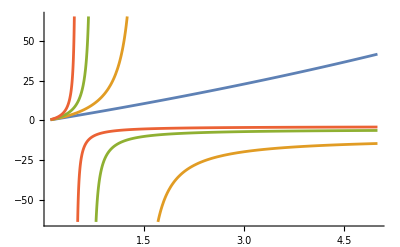

```mathematica
nur = 3.0*10^(17)
myl={nbe[nur,0.005,T], nbe[nur,0.1,T]   ,   nbe[nur,0.2,T] ,   nbe[nur,0.3,T]}
Plot[myl,{T,10*10^6,500*10^6}]
```

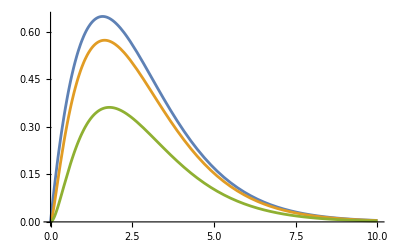

```mathematica
Plot[{x1^2*fbe[x1,0],x1^2*fbe[x1,0.1],x1^2*fbe[x1,0.5]},{x1,0,10}]
```

```mathematica
A=2;
k=1;
x0=1.0;
```

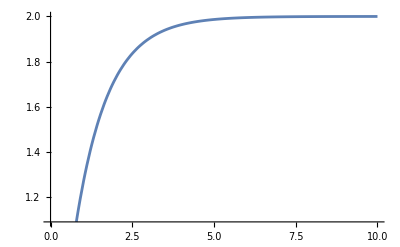

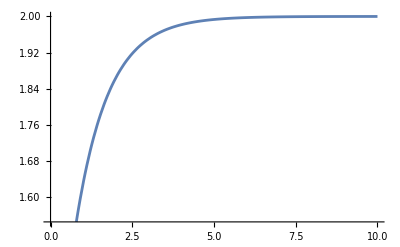

```mathematica
y1[x_]:=A*(x0-Exp[-k*x]);
Plot[y1[x1],{x1,0,10}]
```

## Rates of Change of ni, Te, Tr and Ti CHECK THE UNITS

```mathematica
(**)
f1[t_,ni_,te_,ti_, tr_]:=-(ni^2)*sigvdt[ti];      (* dni/dt *)
f2[t_,ni_,te_,ti_, tr_]:=(2/(3*ne))*((eal*(1-fali[te]))*ni*sigvdt[ti]   +pei[ne,ni,Ni-2*ni,te,ti] - prad[ni,te,ti,tr] );(* dte/dt *) 
f3[t_,ni_,te_,ti_, tr_]:=(2/(3*(ni+ni0)))*((eal*fali[te]+(3*ti/2))*(sigvdt[ti]*ni^2)-pei[ne,ni,Ni-2*ni,te,ti]); (* dti/dt *) 
f4[t_,ni_,te_,ti_, tr_]:=((h*c)^3/(32*Pi*f[al, tr, te ]))*prad[ni,te,ti,tr];      (* dtr/dt *)
```

```mathematica
(**)
niini=1;te0=0.1; ti=0.1;
t0=0;
tf=10;(*final time*)
h=0.1;(*step size*)
```

```mathematica
(**)
(*Runge-Kutta method implementation for the coupled system*)
rk4Step[t_,ni_,te_,ti_, tr_,h_]:=Module[{k1,k2,k3,k4,l1,l2,l3,l4,m1,m2,m3,m4,n1,n2,n3,n4},
k1=h f1[t,ni,te,ti,tr];
l1=h f2[t,ni,te,ti,tr];
m1=h f3[t,ni,te,ti,tr];
n1=h f4[t,ni,te,ti,tr];

k2=h f1[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];
l2=h f2[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];
m2=h f3[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];
n2=h f4[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];

k3=h f1[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];
l3=h f2[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];
m3=h f3[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];
n3=h f4[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];

k4=h f1[t+h,ni+k3,te+l3, ti+m3, tr+n3];
l4=h f2[t+h,ni+k3,te+l3, ti+m3, tr+n3];
m4=h f3[t+h,ni+k3,te+l3, ti+m3, tr+n3];
n4=h f4[t+h,ni+k3,te+l3, ti+m3, tr+n3];

{ni+(k1+2 k2+2 k3+k4)/6,te+(l1+2 l2+2 l3+l4)/6  ,ti+(m1+2 m2+2 m3+m4)/6 ,tr+(n1+2 n2+2 n3+n4)/6  }];
```

```mathematica
(**)
rk4Solve[t0_,niini_,te0_, ti0_,tr0_ ,h_,tf_]:=Module[{t=t0,ni=niini,te=te0, ti=ti0, tr=tr0,sol={{t0,niini,te0, ti0}}},
While[t<tf,
{ni,te,ti,tr}=rk4Step[t,ni,te,ti, tr,h];t=t+h;
AppendTo[sol,{t,ni,te,ti, tr}];];sol];
```

```mathematica
(**)
(*Solve the coupled differential equations*)
solution=rk4Solve[t0,niini,te0,ti0, tr0,h,tf];
(*Extract solutions for x(t) and y(t)*)
nisol=solution[[All,{1,2}]];
tesol=solution[[All,{1,3}]];
tisol=solution[[All,{1,4}]];
trsol=solution[[All,{1,5}]];

(*Plot the solutions*)
ListLinePlot[{nisol,tesol,tisol},PlotMarkers->Automatic,PlotLegends->{"ni(t)","te(t)","ti(t)","tr(t)"},PlotLabels->"Expressions",PlotTheme->"Detailed",AxesLabel->{"t","Value"}]
```